## Data Import

Set this to wherever this file is.

```mathematica
SetDirectory["~/Thesis/Calculations/Angular Momentum/"]
```

/home/ellen/Thesis/Calculations/Angular Momentum

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l0,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
lsplot=Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

There are three data points missing here, as evidenced by the discontinuities in the curves. Instead of going back and taking these data points, I merely shifted the other data points one forward, to make the curves smooth again. The following loop does this.

```mathematica
For[i=22,i≤Length[lsplot[[3]]],i++,
lsplot[[3,i,1]]=i+1;
]
For[i=10,i≤Length[lsplot[[7]]],i++,
lsplot[[7,i,1]]=i+1;
]
For[i=19,i≤Length[lsplot[[6]]],i++,
lsplot[[6,i,1]]=i+1;
]
```

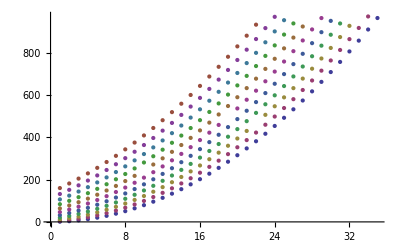

```mathematica
ListPlot[lsplot]
```

## Least Squares Fit

Ls are in the form {n,l}

```mathematica
PolyFit[lambdas_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Inverse[M].{Sum[lambdas[[i,2]],{i,1,Length[lambdas]}],Sum[lambdas[[i,1]]*lambdas[[i,2]],{i,1,Length[lambdas]}],Sum[lambdas[[i,1]]^2*lambdas[[i,2]],{i,1,Length[lambdas]}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
PolyFit[lsplot[[1]]]
```

{A→0.0578679,B→0.0517547,C→0.785389}

```mathematica
Fits=Table[PolyFit[lsplot[[i]]],{i,1,Length[lsplot]}];
```

```mathematica
TableForm[Table[Join[{"l = "<>ToString[i-1]},Fits[[i]]],{i,1,Length[Fits]}]]
```

l = 0 | a→0.0578679 | b→0.0517547 | c→0.785389
l = 1 | a→2.08389 | b→1.87181 | c→0.783359
l = 2 | a→6.69367 | b→3.76342 | c→0.780961
l = 3 | a→13.9713 | b→5.66987 | c→0.778668
l = 4 | a→23.916 | b→7.58959 | c→0.776349
l = 5 | a→36.5385 | b→9.51975 | c→0.774003
l = 6 | a→51.8429 | b→11.4585 | c→0.771512
l = 7 | a→69.8763 | b→13.3975 | c→0.769258
l = 8 | a→90.6213 | b→15.3367 | c→0.767164
l = 9 | a→114.081 | b→17.2771 | c→0.765162
l = 10 | a→140.221 | b→19.2291 | c→0.762649

```mathematica
as=Table[{i-1,a/.Fits[[i,1]]},{i,1,Length[Fits]}]
```

{{0,0.0578679},{1,2.08389},{2,6.69367},{3,13.9713},{4,23.916},{5,36.5385},{6,51.8429},{7,69.8763},{8,90.6213},{9,114.081},{10,140.221}}

```mathematica
bs=Table[{i-1,b/.Fits[[i,2]]},{i,1,Length[Fits]}]
```

{{0,0.0517547},{1,1.87181},{2,3.76342},{3,5.66987},{4,7.58959},{5,9.51975},{6,11.4585},{7,13.3975},{8,15.3367},{9,17.2771},{10,19.2291}}

```mathematica
cs=Table[{i-1,c/.Fits[[i,3]]},{i,1,Length[Fits]}]
```

{{0,0.785389},{1,0.783359},{2,0.780961},{3,0.778668},{4,0.776349},{5,0.774003},{6,0.771512},{7,0.769258},{8,0.767164},{9,0.765162},{10,0.762649}}

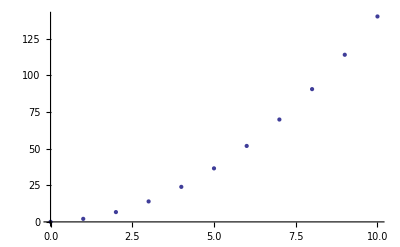

```mathematica
ListPlot[as]
```

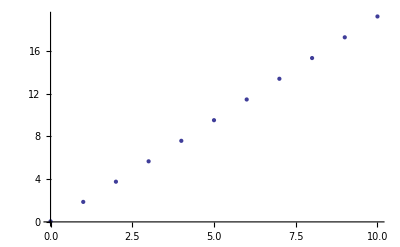

```mathematica
ListPlot[bs]
```

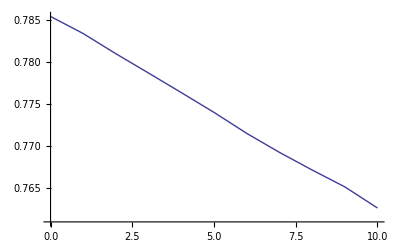

```mathematica
ListPlot[cs,Joined->True]
```